```mathematica
(*GLOBAL INITIALIZATION*)
(*Position of the lost plan*)
distantR = 0.8;

(*
	The position where the plane actually is lost at
	The plane start getting missing at {0,0}
*)
θ=RandomReal[{0,2π}]
lostX = distantR*Cos[θ];
lostY = distantR*Sin[θ];
(*stepDist is the *)
stepDist=0.1;

(*Prec is the range when the object is likely to bedescivered*)
prec = stepDist/2;

(*Range*)
rangeX={-1,1};
rangeY={-1,1};
(*Minimal Probability possible*)
(*minP=1/((rangeX[[2]]-rangeX[[1]])*((rangeY[[2]]-rangeY[[1]]))/stepDist^2*10000);*)
minP=0;
(*Function that change from a position to an index*)
indexOf[x_,y_]:=Module[{},
{Round[(x-(rangeX[[1]]))/stepDist]+1,Round[(y-(rangeY[[1]]))/stepDist]+1}
];
lostIndexP=myindexOf[lostX,lostY];
lostIndexX=lostIndexP[[1]];
lostIndexY=lostIndexP[[2]];

(*Whether to show the update when the searcher is searching something*)
displayDuringSearching=False;
```

4.94872

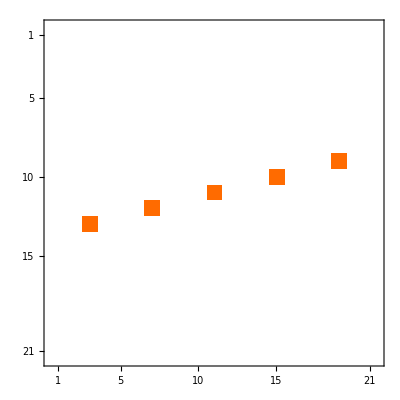
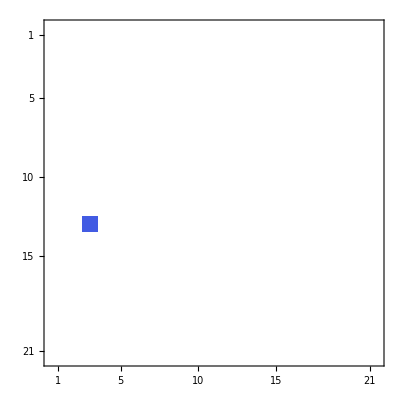
{-Graphics-,-Graphics-,{0.187308,-0.777763}}

```mathematica
(*Simulation Environment*)
(*If the position(x,y) is on the path*)
isOnPath[x_,y_]:=Module[{m=lostY/lostX, expT=prec},
(*Linear Path*)
Abs[x-0]+Abs[x-Cos[ArcTan[m]]*distantR]-1<expT && 
Abs[y-m*x] <expT
];

(*Whether the position is the plane position*)
isFound[x_,y_]:=Module[{rt = prec,lp,lx,ly},
lp=indexOf[x,y];
lx=lp[[1]];
ly=lp[[2]];
lostIndexX==lx && lostIndexY==ly
];

(* The probability that we give evidence when searching at the path*)
pEvidenceFoundOnPath=0.3;

(*Search a particular Point in the map*)
searchMapAtPoint[x_,y_]:=Module[{p=RandomReal[{0,1}] < pEvidenceFoundOnPath},
isOnPath[x,y] && p
];

(*Update the Data At Specific Point*)
changeDataAt[list_,posX_,posY_,newValue_]:=Module[{expT=prec},
Table[
If[
Abs[posX-x]< expT &&Abs[posY-y]<expT,
newValue,
list[[
indexOf[x,y][[1]]
]][[
indexOf[x,y][[2]]
]]
],
{x,rangeX[[1]],rangeX[[2]],stepDist},
{y,rangeY[[1]],rangeY[[2]],stepDist}
]
];
planePathData = Table[If[isOnPath[x,y],1,0],{x,-1,1,stepDist},{y,-1,1,stepDist}];
plotLostPlane =Table[0,{x,-1,1,stepDist},{y,-1,1,stepDist}];
plotLostPlane= changeDataAt[plotLostPlane,lostX,lostY,-100];
{
(*ListDensityPlot[planePathData,PlotRange->All],
ListDensityPlot[data,PlotRange->All],*)
MatrixPlot[planePathData,PlotRange->All],
MatrixPlot[plotLostPlane,PlotRange->All],
{lostX,lostY}
}
```

```mathematica
SearcherModel[objectData_,searcherDataInit_]:=Module[{
(* 
	searcher data is the probability density of the 
	probability that the searcher can find the object
	given that the object is in the position
	P(D|O)
*)
searcherData,

(* 
	data is the probability density of the 
	probability that if the object is in the position
	and given that we can detected it
	P(D|O)*P(O)=P(O|D)
*)
initData,
(*Generate the Initial Data*)
data,

(*Searching Algorithm Functions*)
failSearchProbability,
failUnsearchProbability,
getSearchPoint,
searchPoint,
plotData
},

(* has to manually initialize *)
searcherData= Table[
searcherDataInit[x,y],
{x,rangeX[[1]],rangeX[[2]],stepDist},
{y,rangeY[[1]],rangeY[[2]],stepDist}
];

(***********************)
(* has to manually initialize *)
data=objectData*searcherData;

(* Updates the object probability at position (x,y) when unfound *)
failSearchProbability[x_,y_]:=Module[{
ix=indexOf[x,y][[1]], iy=indexOf[x,y][[2]],
poo=0,pdo=0,ret
},
poo=objectData[[ix]][[iy]];
pdo=searcherData[[ix]][[iy]];
ret=(poo*Abs[1-pdo])/(1-poo*pdo);

If[ret<minP,minP,ret]
];

(* Updates the object probability at position(x,y) unsearched *)
failUnsearchProbability[x_,y_,xo_,yo_]:=Module[{
ix=indexOf[x,y][[1]], iy=indexOf[x,y][[2]],
ixo=indexOf[xo,yo][[1]], iyo=indexOf[xo,yo][[2]],
poo=0,pdo=0,qoo=0,ret
},
qoo=objectData[[ix]][[iy]];
poo=objectData[[ixo]][[iyo]];
pdo=searcherData[[ixo]][[iyo]];
ret =(qoo/(1-poo*pdo));
If[ret<minP,minP,ret]
];

(* Found the next search point *)
getSearchPoint[list_]:=Module[{
max=-Infinity,
x=rangeX[[1]], y=rangeY[[1]],
mx=0,my=0,ix,iy
},
While[x-rangeX[[2]] < prec,
While[y-rangeY[[2]] < prec,
ix=indexOf[x,y][[1]];
iy=indexOf[x,y][[2]];
If[
max<list[[ix]][[iy]],
max=list[[ix]][[iy]];
mx=x;
my=y;
(*Print[{max,list[[ix]][[iy]], {ix,iy},{x,y},{px,py}}]*);
];
y+=stepDist;
];
y=rangeY[[1]];
x+=stepDist;
];
Return[{mx,my}];
];
searchPoint =getSearchPoint[data];
plotData= changeDataAt[data,searchPoint[[1]],searchPoint[[2]],-1];
If[displayDuringSearching,
Print[{MatrixPlot[data],MatrixPlot[objectData],MatrixPlot[searcherData],MatrixPlot[plotData]}];
Print[{
ListPointPlot3D[data,PlotRange->All,ColorFunction->Function[{x,y,z},Hue[-z]]],
ListPointPlot3D[objectData,PlotRange->All,ColorFunction->Function[{x,y,z},Hue[-z]]],
ListPointPlot3D[searcherData,PlotRange->All,ColorFunction->Function[{x,y,z},Hue[-z]]],
ListPlot3D[plotData,PlotRange->All,ColorFunction->Function[{x,y,z},Hue[z]]]}
];
];

(*Return[Apply[isFound,searchPoint]];*)
Return[
<|
ret->Apply[isFound,searchPoint],
pos->searchPoint,
posIndex->Apply[indexOf,searchPoint],
pdo-> searcherData[[Apply[indexOf,searchPoint][[1]]]][[Apply[indexOf,searchPoint][[2]]]],
poo-> data[[Apply[indexOf,searchPoint][[1]]]][[Apply[indexOf,searchPoint][[2]]]]
|>
];
];
```

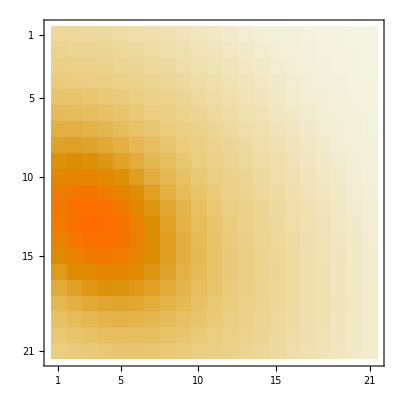
{-Graphics3D-,-Graphics-}

```mathematica
(***********************)
(* Object Data *)
(* precondition:  0<ρ<1 *)
objectDataInit[x_,y_]:=Module[{ρ=0.3,σx=0.3,σy=0.3},
PDF[MultinormalDistribution[{lostX,lostY},{{σx^2,ρ*σx*σy},{ρ*σx*σy,σy^2}}],{x,y}]*stepDist^2
];

(* has to manually initialize *)
objectData=Table[
objectDataInit[x,y],
{x,rangeX[[1]],rangeX[[2]],stepDist},
{y,rangeY[[1]],rangeY[[2]],stepDist}
];

Print[{
DiscretePlot3D[objectDataInit[x,y],{x,rangeX[[1]],rangeX[[2]],stepDist},{y,rangeY[[1]],rangeY[[2]],stepDist},ExtentSize->stepDist],
MatrixPlot[objectData]
}];
```

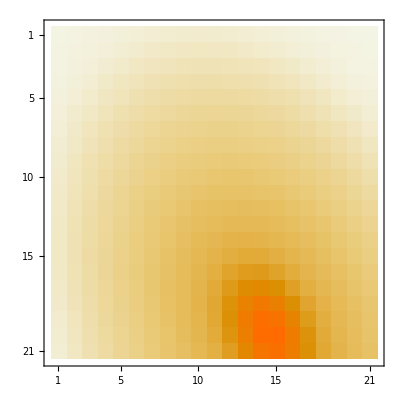
{-Graphics3D-,-Graphics-}

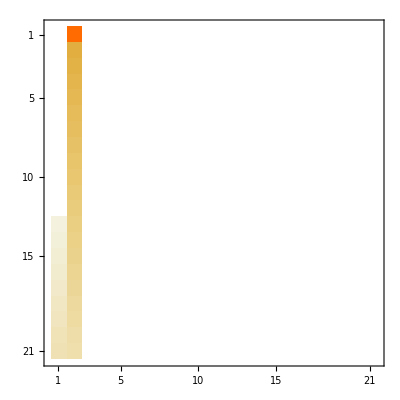
{-Graphics3D-,-Graphics-}

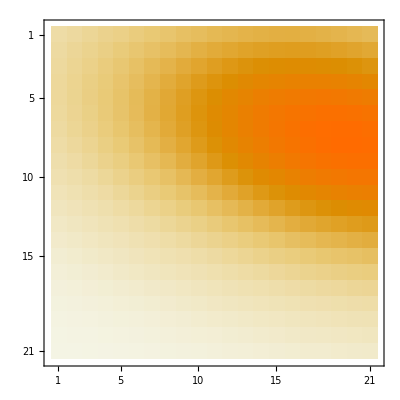
{-Graphics3D-,-Graphics-}

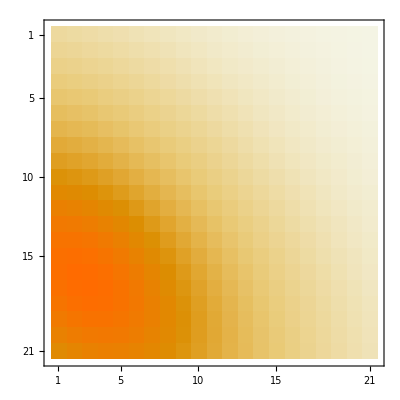
{-Graphics3D-,-Graphics-}

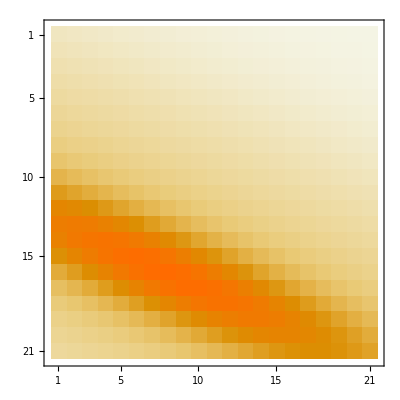
{-Graphics3D-,-Graphics-}

```mathematica
(*FUnction that display data pdf*)
printDataPDF[pdf_]:=Module[{tmp},
tmp=Table[pdf[x,y],{x,rangeX[[1]],rangeX[[2]],stepDist},{y,rangeY[[1]],rangeY[[2]],stepDist}];
Print[{
DiscretePlot3D[pdf[x,y],{x,rangeX[[1]],rangeX[[2]],stepDist},{y,rangeY[[1]],rangeY[[2]],stepDist},ExtentSize->stepDist],
MatrixPlot[tmp]
(*tmp*)
}];
];

(* {cx,cy} is the initial center of the searcher *)
(* precondition:  0<ρ<1 *)
generateSearcherData[centerX_,centerY_,a_,bx_,by_]:=Module[
{},
Function[{x,y},PDF[MultinormalDistribution[{centerX,centerY},{{bx^2,a*bx*by},{a*bx*by,by^2}}],{x,y}]*stepDist^2]
];

For[i=0,i<5,i++,Module[{para},
para=Map[Function[x,RandomReal[x]],{{-1,1},{-1,1},{-1,1},{0,1},{0,1}}];
printDataPDF[Apply[generateSearcherData,para]];
]];
(*printDataPDF[searcherDataInitOne];*)
```

```mathematica
(*res=SearcherModel[objectData,generateSearcherData[0.3,0.3,0.3,0.5,0.5]]*)
```

```mathematica
(* Generate Searchers *)
searchers={};
For[i=0,i<5,i++,Module[{para},
para=Map[Function[x,RandomReal[x]],{{-1,1},{-1,1},{-1,1},{0,1},{0,1}}];
searchers=Append[searchers,Apply[generateSearcherData,para]];
]];

(* Let a list of searchers to search with a particular condition *)
allSearch[searchers_,objectData_]:=Module[{searchResults},
searchResults={};
For[i=0,i<Length[searchers],i++,Module[{},
searchResults=Append[searchResults,SearcherModel[objectData,searchers[[i+1]]]];
]];
searchResults
];

(*searchResults=allSearch[searchers,objectData]*)
```

```mathematica
(* Incorproate the search result to generate a new update*)

(* test whether the search is successful *)
isSuccessful[result_]:=Module[{extr},
extr[a_]:=a[ret];(*extract certain data*)
Fold[Or,False,Map[extr,result]]
];
(*isSuccessful[searchResults]*)
```

```mathematica
(*Flatter the list so that I know what are the position that the searcher searched*)
restracture[result_]:=Module[{restruct},
restruct[a_]:={a[posIndex],a[poo]*a[pdo],a[poo]*(1-a[pdo])};
Map[restruct,result]
];
(*restracture[searchResults]*)
```

```mathematica
calculateDenominator[restruct_]:=Module[{},
Fold[Function[{x,y},x-y],1,restruct][[2]]
];
(*denominator = calculateDenominator[restracture[searchResults]]*)
```

```mathematica
reduceColumneProduct[restruct_,denominator_]:=Module[{},
Map[Function[x,{x[[1]],x[[3]]/denominator}],restruct]
];
(*restruct=reduceColumneProduct[restracture[searchResults],denominator]*)
```

```mathematica
(* Function to check whether contains *)
restructContains[result_,{px_,py_}]:=Module[{},
Fold[
Function[{prev,current},
prev || current[[1]] == {px,py}
],False,result]
];
(*{restructContains[restruct,{17,11}],restructContains[restruct,{13,11}]}*)
```

```mathematica
(*
Extract result from the structure 
TODO! should I make it return ZERO? which is safer?
*)
extractRestruct[result_,{px_,py_}]:=Module[{},
Fold[Function[{prev,current},
If[prev==-Infinity &&current[[1]] == {px,py},current[[2]],prev]
],-Infinity,result]
];
(*{extractRestruct[restruct,{13,11}],extractRestruct[restruct,{17,11}]}*)
```

```mathematica
(* Generate a new List *)
updateObjectProbabilityAfterFail[result_,denominator_,originalObjectData_ ]:=Module[{tmp,f},
f[x_,y_]:=Module[{pos},
pos=indexOf[x,y];
If[
restructContains[result,pos],
extractRestruct[result,pos],
originalObjectData[[pos[[1]]]][[pos[[2]]]]/denominator
 ]
];
Return[Table[f[x,y],{x,rangeX[[1]],rangeX[[2]],stepDist},{y,rangeY[[1]],rangeY[[2]],stepDist}]]
];
(*{MatrixForm[restruct],MatrixPlot[objectData],denominator,MatrixPlot[updateObjectProbabilityAfterFail[restruct,denominator, objectData]]}*)
```

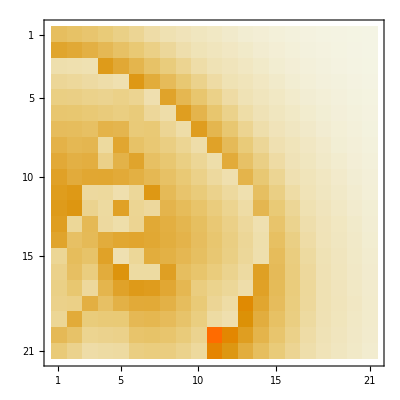
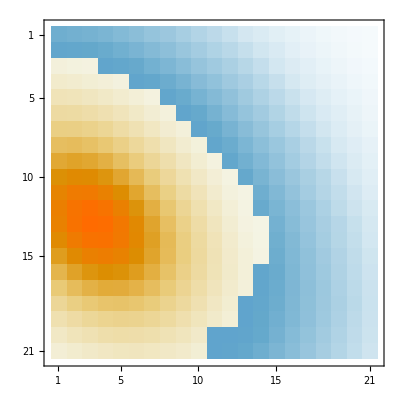
{-Graphics-,-Graphics-,-Graphics-}

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

(<|ret→False,pos→{0.5,-0.5},posIndex→{16,6},pdo→0.00635468,poo→3.51459×10^-7|>
<|ret→False,pos→{-0.6,-0.4},posIndex→{5,7},pdo→0.00268076,poo→1.58995×10^-7|>
<|ret→False,pos→{-0.8,-0.8},posIndex→{3,3},pdo→0.00205729,poo→1.07276×10^-7|>
<|ret→False,pos→{0.1,-0.7},posIndex→{12,4},pdo→0.0134049,poo→3.83531×10^-7|>
<|ret→False,pos→{0.2,0.3},posIndex→{13,14},pdo→0.00873403,poo→1.41538×10^-7|>)

```mathematica
multiSearcherSearch[initObjectData_,searchers_,max_]:=Module[{diff=initObjectData,data=initObjectData,searchResults=False,originalData,restruct,denominator,restructSearchRet,t},
t=0;
Monitor[
While[t==0||!isSuccessful[searchResults] && t<max,
originalData=data;
(*Print[MatrixPlot[originalData]];*)

(*get the search result*)
searchResults=allSearch[searchers,originalData];
(*Print[MatrixForm[searchResults]];*)

restructSearchRet=restracture[searchResults];
(*Print[restructSearchRet];*)

denominator=calculateDenominator[restructSearchRet];
(*Print[denominator];*)

restruct=reduceColumneProduct[restructSearchRet,denominator];
(*Print[restruct];*)

data=updateObjectProbabilityAfterFail[restruct,denominator, originalData];
diff=originalData- data ;
t++;
],{MatrixPlot[originalData],MatrixPlot[data],MatrixPlot[diff],t}];

Print[{MatrixPlot[initObjectData],MatrixPlot[data], MatrixPlot[initObjectData-data]}];Print[{ListPlot3D[initObjectData,PlotRange->All], ListPlot3D[data,PlotRange->All],ListPlot3D[initObjectData-data,PlotRange->All]}];
Print[MatrixForm[searchResults]];
];

multiSearcherSearch[objectData,searchers,50]
```